```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
Print["Runs in the list: runNum = ",runNum={12693}]
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: runNum = {12693}

#Runs in the list: runn = 1

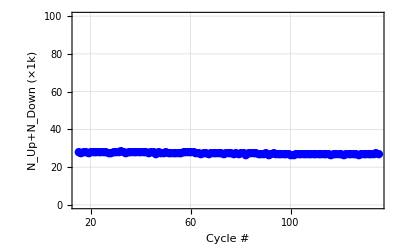
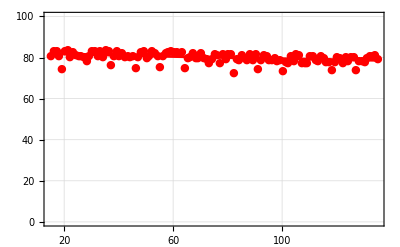

```mathematica
runi=1;
data=ReadList[StringJoin[ScrDir,"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2];
begCy=15;
maxCy=135;
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ftud=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/1000},{k,begCy,maxCy}];
ftmon=Table[{data[[k]][[2]],(data[[k]][[30]])/10000},{k,begCy,maxCy}];
nlmud=NonlinearModelFit[ftud,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
nlmmon=NonlinearModelFit[ftmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
pt1=Show[{Plot[nlmud[x],{x,begCy,maxCy},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Blue,Thickness[.005]},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptud,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt2=Show[{
EDAListPlot[ptmon,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[nlmmon[x],{x,begCy,maxCy},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Red,Thickness[.005]},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}]
},ImagePadding->125];
pt3=Overlay[{pt1,pt2},ImageSize->1200]
```

```mathematica
nlmmon["ParameterTable"]
nlmmon["ANOVATable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
aa | 73.4274 | 22.544 | 3.25707 | 0.00147004
bb | 9.01303 | 21.6682 | 0.415957 | 0.678197
cc | 0.00404225 | 0.0135823 | 0.297612 | 0.766523

| DF | SS | MS
Model | 3 | 777413. | 259138.
Error | 118 | 570.056 | 4.83099
Uncorrected Total | 121 | 777983. | 
Corrected Total | 120 | 678.629 |

```mathematica
ptdatratio2=Select[ptdatratio,((#[[2]][[1]]>.115)&&(#[[2]][[1]]<.14))&];
rmsptdatratio=Mean[ptdatratio2[[;;,2]][[;;,1]]];
sdptdatratio=StandardDeviation[ptdatratio2[[;;,2]][[;;,1]]];
errptsptres=ptdatratio2[[;;,2]][[;;,1]]-rmsptdatratio;
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down) / (N_Monitor) Residual","#"},Axes->False,PlotRange->{{-0.025,0.025},{0,2000}},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}],Plot[20PDF[NormalDistribution[0,sdptdatratio],x],{x,-0.025,0.025},Axes->False,PlotRange->{{-0.025,0.025},{0,2000}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down) / (N_Monitor) Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-0.025,0.025},{0,2000}}, Frame->True,FrameLabel->{"(N_Up + N_Down) / (N_Monitor) Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}]
}];
```

```mathematica
URLFetch["https://nedmpsi.atlassian.net/wiki/spaces/nedmcoll/pages/114357200/NStar+data+summary+September+2017"]
```

<!DOCTYPE html><html lang="en"><head><meta charset="utf-8"><meta name="viewport" content="width=device-width,initial-scale=1"><link rel="shortcut icon" href="https://cpfs-cdn.atlassian.com/assets/shared/id-summit/id-summit-aa-favicon.ico"><title>Atlassian account</title><link href="https://common-admin-cdn.atlassian.com/atlassian-id/front-end/1.2.34/static/css/main.643280c9.css" rel="stylesheet"></head><body data-app-state="{&quot;contextPath&quot;:&quot;&quot;,&quot;appConfig&quot;:{&quot;auth0Config&quot;:{&quot;clientId&quot;:&quot;tDP5by46cc3gEck7d2vbHZsqsfrDK6t9&quot;,&quot;tenant&quot;:&quot;atlassian-account-prod&quot;,&quot;domain&quot;:&quot;auth.atlassian.com&quot;,&quot;tokenIssuer&quot;:&quot;https://atlassian-account-prod.pus2.auth0.com&quot;,&quot;callbackUrl&quot;:&quot;https://id.atlassian.com/login/callback&quot;},&quot;confluenceAppId&quot;:&quot;1006971684&quot;,&quot;isSamlEnabled&quot;:true,&quot;recaptchaKeySite&quot;:&quot;6LewHQcTAAAAAJgaYVKlQOahz4gnQME8wqUA0z0J&quot;,&quot;jiraAppId&quot;:&quot;1006972087&quot;,&quot;recaptchaEnable&quot;:true,&quot;isGoogleAuthEnabled&quot;:true,&quot;googleAuthClientId&quot;:&quot;596149463257-9oquqfivs9on8t8erq23c8qso6vk3cp1.apps.googleusercontent.com&quot;},&quot;featureFlags&quot;:{&quot;aid_signup.adg3.enabled&quot;:&quot;true&quot;,&quot;aid_signup.auth0.frontend.login.enabled&quot;:&quot;true&quot;,&quot;kermit.reloaded&quot;:&quot;true&quot;},&quot;csrfToken&quot;:&quot;369ab5235197d2121b468b0c3bc1a9a8a8377433&quot;,&quot;microbranding&quot;:{&quot;isEmbedded&quot;:&quot;false&quot;}}"><div id="root"></div><script>var mfaServerUrl="",ticket="",requestToken="",postActionURL="",userData={userId:"",email:"",friendlyUserId:"",tenant:"",tenantFriendlyName:""},globalTrackingId=""</script><script type="text/javascript" src="https://common-admin-cdn.atlassian.com/atlassian-id/front-end/1.2.34/static/js/main.b24072ff.js"></script></body></html>